# Multiple shooting method for intersection numbers

The authors of this code are
Yutaro Shoji and Katarina Trailović.
Please cite the following paper:
“Stable Evaluation of Lefschetz Thimble Intersection Numbers: Towards Real-Time Path Integrals”, Y. Shoji and K. Trailović, 2510.06334[hep-th].
yutaro.shoji@ijs.si
katarina.trailovic@ijs.si

## Multiple shooting method

```mathematica
RandomInitial[zstar_,Nseg_,δr_]:=Block[{randvec,ZInit,dsInit,L},L=Length[zstar];
randvec=Normalize[RandomReal[NormalDistribution[],L]];
dsInit=10^(-2*RandomReal[]);
ZInit=Table[{Re[zstar+randvec ((i-1) dsInit+δr)],Im[zstar+randvec ((i-1) dsInit+δr)]},{i,Nseg}];
{ZInit,dsInit}];
```

```mathematica
MultipleShooting[Iaction_,zstar_,Nseg_,δr_,sens_,maxIterations_,ZInit_,dsInit_,δ_,q_]:=Block[{L,zstarReIm,zv,eval,evec,negindex,posindex,Wm,Wp,gradReIm,eqns,variab,inits,ϕsol,WΛW,X,mat01,c,RA0f,RA0,RB0f,RB0,RBNf,RBN,Rtabf,Rtab,Rtotf,Rtot,time,δindex,Jz,Js,Jzcurltab,Jscurltab,Rcurltab,ΔZ0,Δds,M0pds,Arr,ΔZ,ΔX,ErrRA0,ErrRtab,ErrRB0,ErrRBN,α,nσ},

L=Length[zstar];
zstarReIm={Re[zstar],Im[zstar]};
zv=Array[z,L];

(*Hessian at the saddle point*)
{eval,evec}=Block[{M,A},
M=D[Iaction,{zv,2}]/.Thread[zv->zstar];
A=ArrayFlatten[{{Re[M],-Im[M]},{-Im[M],-Re[M]}}];
Eigensystem[A]];

negindex=Flatten@Position[eval,_?Negative];
posindex=Complement[Range[2L],negindex];
Wm=evec[[negindex]]ᵀ;
Wp=evec[[posindex]]ᵀ;


(*Differential equations*)
gradReIm=Block[{grad},
grad=D[Iaction,{zv}]/.{z[i_]->x[i]+I y[i]};
{ComplexExpand[Re[grad]],ComplexExpand[Im[grad]]}/.{x[i_]->x[i][u],y[i_]->y[i][u]}];
eqns=Table[{x[i]'[u]==(gradReIm[[1]][[i]])/Norm[Flatten[gradReIm]],y[i]'[u]==(-gradReIm[[2]][[i]])/Norm[Flatten[gradReIm]]},{i,L}];
variab={Array[x,L],Array[y,L]};
inits[Fk_]:=Table[{x[i][0]==Fk[[1]][[i]],y[i][0]==Fk[[2]][[i]]},{i,L}];
ϕsol[Fk_,s_,smax_]:={Table[x[i][s],{i,1,L}],Table[y[i][s],{i,1,L}]}/.NDSolve[Flatten[{eqns,inits[Fk]}],Flatten[variab],{u,0,smax},Method->"ExplicitEuler",StartingStepSize->smax/10][[1]];


(*Modified anchor condition*)
WΛW=Block[{Λq,W},
Λq=DiagonalMatrix[Flatten[{Abs[eval[[negindex]]]/Min[Abs[eval[[negindex]]]],Abs[eval[[posindex]]]/Min[Abs[eval[[posindex]]]]}]^q];
W=Join[Wmᵀ,Wpᵀ]ᵀ;
W.Λq.Wᵀ];

(*Initialize*)
X=Append[ZInit,dsInit];

(*Projection to imaginary*)
mat01=ArrayFlatten[{{ConstantArray[0,{L,L}],IdentityMatrix[L]}}];

(*Initial value of line search parameter*)
c=Infinity;

(*Residual vectors*)
RA0f[x_]:=Norm[WΛW.Flatten[x[[1]]-zstarReIm]]-δr;
RB0f[x_]:=Wmᵀ.Flatten[x[[1]]-zstarReIm];
RBNf[x_]:=x[[Nseg]][[2]];
Rtabf[x_]:=ParallelTable[x[[k]]-ϕsol[x[[k-1]],Abs[x[[Nseg+1]]],Abs[x[[Nseg+1]]]],{k,2,Nseg}];
Rtotf[x_]:=Norm[Flatten[{RA0f[x],RB0f[x],Rtabf[x],RBNf[x]}]];

Do[
time=SessionTime[];

(*Current residual vectors*)
RA0=RA0f[X];
RB0=RB0f[X];
RBN=RBNf[X];
Rtab=Rtabf[X];
Rtot=Rtotf[X];

(*Jacobians*)
δindex=Flatten[Table[{i,j},{i,1,2},{j,1,L}],1];
Jz=ParallelTable[Transpose[Table[Flatten[1/(2δ)(ϕsol[X[[k]]+δ SparseArray[{ij->1},{2,L}],X[[Nseg+1]],X[[Nseg+1]]]-ϕsol[X[[k]]-δ SparseArray[{ij->1},{2,L}],X[[Nseg+1]],X[[Nseg+1]]])],{ij,δindex}]],{k,1,Nseg}];
Js=ParallelTable[Flatten[D[ϕsol[X[[k]],s,X[[Nseg+1]]],s]/.{s->X[[Nseg+1]]}],{k,1,Nseg}];

(*Solve recursive relations*)
Jzcurltab={};
Block[{Jzcurl=IdentityMatrix[2 L]},
Do[{Jzcurl=Jz[[k]].Jzcurl,Jzcurltab=Append[Jzcurltab,Jzcurl]},{k,1,Nseg-1}]];

Jscurltab={Js[[1]]};
Block[{Jscurl=Js[[1]]},
Do[{Jscurl=Js[[k]]+Jz[[k]].Jscurl,Jscurltab=Append[Jscurltab,Jscurl]},{k,2,Nseg-1}]];

Rcurltab={Flatten[Rtab[[1]]]};
Block[{Rcurl=Flatten[Rtab[[1]]]},
Do[{Rcurl=Flatten[Rtab[[k]]]+Jz[[k]].Rcurl,Rcurltab=Append[Rcurltab,Rcurl]},{k,2,Nseg-1}]];

(*Solve the linear system*)
{ΔZ0,Δds}=Block[{DRA0,ΔZ0pds,ΔZ0p,ΔZ0m},DRA0=(WΛW.WΛW.Flatten[X[[1]]-zstarReIm])/Norm[WΛW.Flatten[X[[1]]-zstarReIm]];
M0pds=Append[MapThread[Append,{mat01.Jzcurltab[[Nseg-1]].Wp,mat01.Jscurltab[[Nseg-1]]}],Append[DRA0.Wp,0]];
Arr=Append[mat01.(Rcurltab[[Nseg-1]]+Jzcurltab[[Nseg-1]].Wm.RB0)-RBN,DRA0.Wm.RB0-RA0];
ΔZ0pds=Quiet[LinearSolve[M0pds,Arr]];
ΔZ0p=ΔZ0pds[[1;;L]];
ΔZ0m=-RB0;
{Wp.ΔZ0p+Wm.ΔZ0m,ΔZ0pds[[L+1]]}
];


(*Compute ΔX*)
ΔZ=Table[Jzcurltab[[k]].ΔZ0+Jscurltab[[k]] Δds-Rcurltab[[k]],{k,1,Nseg-1}];
ΔX=Append[ArrayFlatten[{{{ΔZ0[[1;;L]],ΔZ0[[L+1;;2L]]}},Table[{ΔZ[[i]][[1;;L]],ΔZ[[i]][[L+1;;2L]]},{i,1,Nseg-1}]},1],Δds];

(*Errors*)
ErrRA0=((WΛW.WΛW.Flatten[X[[1]]-zstarReIm])/Norm[WΛW.Flatten[X[[1]]-zstarReIm]]).ΔZ0+RA0;
ErrRtab=Table[Flatten[ΔX[[k]]]-Jz[[k-1]].Flatten[ΔX[[k-1]]]-Js[[k-1]]Δds+Flatten[Rtab[[k-1]]],{k,2,Nseg}];
ErrRB0=Table[Wmᵀ[[i]].ΔZ0+RB0[[i]],{i,1,L}];
ErrRBN=mat01.Flatten[ΔX[[Nseg]]]+RBN;

(*Line search*)
If[Mod[icount,5]==0,c=If[c==Infinity,1,Infinity]];
α=1;
If[Rtotf[X+α ΔX]>c*Rtot,While[α>0.01&&Rtotf[X+α ΔX]>c *Rtot,α=α*0.5]];

(*Update*)
X=X+α ΔX;
X[[Nseg+1]]=Abs[X[[Nseg+1]]];
Rtot=Rtotf[X];

(*Intersection number*)
nσ=Sign[Det[Join[Wmᵀ,Wpᵀ]ᵀ]]Sign[Det[ArrayFlatten[{{IdentityMatrix[L],ConstantArray[0,{L,L}]}}].Jzcurltab[[Nseg-1]].Wp]];

PrintTemporary["Timing: ",SessionTime[]-time];
PrintTemporary["Current Rtot: ",Rtot];
PrintTemporary["Newton error: Rk, RA0, RB0, RBN: ", {Norm[Flatten[ErrRtab]],Norm[ErrRA0], Norm[Flatten[ErrRB0]],Norm[Flatten[ErrRBN]]}];
PrintTemporary["|Inverse.Matrix-1|: ", Norm[Flatten[Quiet[Inverse[M0pds]].M0pds-IdentityMatrix[L+1]]]];
PrintTemporary["Sign of nσ: ", nσ];
PrintTemporary["W_-: ", Wm];
PrintTemporary[" "];

If[sens>Rtot||icount==maxIterations,Return[{X[[;;-2,1]]+I X[[;;-2,2]],X[[-1]],Rtot,nσ,Wm}]];
,{icount,maxIterations}]
]
```

## Three-variable Airy integral

```mathematica
data=Block[{α=2.62,index=6,Nseg=50,δr=0.1,sens=10^(-13),maxIter=30,δ=0.01,q=1.5,c0,c1,c2,Iaction,zstartable,zstar,Sol,ZInit,dsInit,dIdz},
c0=0.5* Exp[I* α];
c1=0.5* Exp[I* 2 * α];
c2=0.5 *Exp[I* 3 * α];
Iaction=I ((z[1]^3+z[2]^3+z[3]^3)/3-z[1]z[2]-z[2]z[3]-z[3]z[1]+c0 z[1]+c1 z[2]+c2 z[3]);
(*Computing all saddle points*)
zstartable=Array[z,3]/.NSolve[D[Iaction,{Array[z,3]}]==0,Array[z,3]];

(*choosing one saddle point*)
zstar=zstartable[[index]];

{ZInit,dsInit}=RandomInitial[zstar,Nseg,δr];
Sol=MultipleShooting[Iaction,zstar,Nseg,δr,sens,maxIter,ZInit,dsInit,δ,q];

(*Gradient of I*)
dIdz={D[Iaction,z[1]],D[Iaction,z[2]],D[Iaction,z[3]]};

{Sol,zstar,dIdz}
]
```

{{{{-0.120621+0.02623 ⅈ,-0.0753077+0.839469 ⅈ,-0.335807-0.569842 ⅈ},{-0.101849+0.0323016 ⅈ,-0.0655321+0.833121 ⅈ,-0.347715-0.556445 ⅈ},{-0.0829107+0.0382159 ⅈ,-0.0561597+0.826723 ⅈ,-0.35959-0.542917 ⅈ},{-0.0639051+0.0437441 ⅈ,-0.046822+0.820228 ⅈ,-0.371327-0.529222 ⅈ},{-0.0448871+0.0488207 ⅈ,-0.0374512+0.813591 ⅈ,-0.382871-0.515298 ⅈ},{-0.0258911+0.0534129 ⅈ,-0.0280296+0.806764 ⅈ,-0.394176-0.50111 ⅈ},{-0.00694631+0.0574993 ⅈ,-0.0185536+0.799697 ⅈ,-0.4052-0.486633 ⅈ},{0.0119172+0.0610648 ⅈ,-0.009025+0.792343 ⅈ,-0.415902-0.471853 ⅈ},{0.0306664+0.0640998 ⅈ,0.000552066+0.784652 ⅈ,-0.426249-0.456761 ⅈ},{0.0492639+0.0666003 ⅈ,0.0101723+0.776575 ⅈ,-0.436208-0.441356 ⅈ},{0.0676679+0.0685679 ⅈ,0.0198301+0.768064 ⅈ,-0.445758-0.425643 ⅈ},{0.0858318+0.0700108 ⅈ,0.0295198+0.759071 ⅈ,-0.454885-0.409632 ⅈ},{0.103705+0.0709435 ⅈ,0.0392362+0.749547 ⅈ,-0.463585-0.393345 ⅈ},{0.121234+0.0713866 ⅈ,0.0489747+0.739444 ⅈ,-0.471867-0.376809 ⅈ},{0.138361+0.0713664 ⅈ,0.0587319+0.728714 ⅈ,-0.479753-0.360059 ⅈ},{0.155027+0.0709134 ⅈ,0.068505+0.717311 ⅈ,-0.487278-0.34314 ⅈ},{0.171172+0.0700617 ⅈ,0.078292+0.705188 ⅈ,-0.494489-0.326104 ⅈ},{0.186735+0.0688475 ⅈ,0.0880913+0.692302 ⅈ,-0.501445-0.309008 ⅈ},{0.201655+0.0673084 ⅈ,0.0979015+0.678615 ⅈ,-0.508211-0.29192 ⅈ},{0.215874+0.0654824 ⅈ,0.107721+0.664095 ⅈ,-0.514858-0.274908 ⅈ},{0.229337+0.0634072 ⅈ,0.117548+0.648719 ⅈ,-0.521459-0.258049 ⅈ},{0.241994+0.06112 ⅈ,0.127379+0.632477 ⅈ,-0.528082-0.241417 ⅈ},{0.253799+0.0586572 ⅈ,0.137211+0.615371 ⅈ,-0.534793-0.225089 ⅈ},{0.264718+0.0560536 ⅈ,0.14704+0.597419 ⅈ,-0.54165-0.209139 ⅈ},{0.274724+0.0533426 ⅈ,0.156863+0.578652 ⅈ,-0.5487-0.193632 ⅈ},{0.283801+0.0505553 ⅈ,0.166675+0.559112 ⅈ,-0.555981-0.178629 ⅈ},{0.291944+0.0477208 ⅈ,0.176475+0.538854 ⅈ,-0.563522-0.164182 ⅈ},{0.299157+0.0448652 ⅈ,0.186261+0.51794 ⅈ,-0.57134-0.150331 ⅈ},{0.305455+0.042012 ⅈ,0.196032+0.496435 ⅈ,-0.579445-0.137107 ⅈ},{0.310858+0.0391815 ⅈ,0.205791+0.474407 ⅈ,-0.587842-0.12453 ⅈ},{0.315393+0.0363914 ⅈ,0.215541+0.451923 ⅈ,-0.596526-0.112614 ⅈ},{0.319092+0.0336564 ⅈ,0.225285+0.429048 ⅈ,-0.605493-0.101363 ⅈ},{0.321989+0.0309886 ⅈ,0.235028+0.405843 ⅈ,-0.614733-0.0907756 ⅈ},{0.32412+0.0283979 ⅈ,0.244777+0.382366 ⅈ,-0.624236-0.0808456 ⅈ},{0.32552+0.0258922 ⅈ,0.254538+0.358668 ⅈ,-0.633989-0.0715633 ⅈ},{0.326226+0.0234774 ⅈ,0.264317+0.334796 ⅈ,-0.64398-0.0629162 ⅈ},{0.326273+0.021158 ⅈ,0.274122+0.310795 ⅈ,-0.654198-0.05489 ⅈ},{0.325693+0.0189371 ⅈ,0.283959+0.286702 ⅈ,-0.66463-0.0474694 ⅈ},{0.324521+0.0168168 ⅈ,0.293835+0.262551 ⅈ,-0.675265-0.0406384 ⅈ},{0.322786+0.0147982 ⅈ,0.303755+0.238374 ⅈ,-0.686092-0.0343811 ⅈ},{0.320517+0.0128814 ⅈ,0.313727+0.214198 ⅈ,-0.697101-0.0286812 ⅈ},{0.317743+0.0110663 ⅈ,0.323756+0.190048 ⅈ,-0.708283-0.023523 ⅈ},{0.31449+0.00935173 ⅈ,0.333846+0.165946 ⅈ,-0.719628-0.0188911 ⅈ},{0.310782+0.0077363 ⅈ,0.344002+0.141911 ⅈ,-0.73113-0.0147704 ⅈ},{0.306642+0.00621816 ⅈ,0.35423+0.117962 ⅈ,-0.742779-0.0111464 ⅈ},{0.302094+0.00479509 ⅈ,0.364531+0.0941144 ⅈ,-0.75457-0.00800501 ⅈ},{0.297158+0.0034646 ⅈ,0.374911+0.0703823 ⅈ,-0.766495-0.00533266 ⅈ},{0.291854+0.00222393 ⅈ,0.385372+0.0467785 ⅈ,-0.778549-0.00311615 ⅈ},{0.286201+0.00107011 ⅈ,0.395916+0.0233143 ⅈ,-0.790726-0.00134273 ⅈ},{0.280219-3.77302×10^-17 ⅈ,0.406545-4.85723×10^-17 ⅈ,-0.803021+2.08167×10^-17 ⅈ}},0.0290942,1.1964×10^-7,1,{{-0.263712,0.51209,0.300193},{-0.678572,-0.587363,-0.239396},{-0.179775,0.0932255,0.4228},{0.312681,0.257752,-0.643349},{0.122578,-0.16562,-0.30786},{0.569984,-0.538712,0.406372}}},{-0.185246-0.00197422 ⅈ,-0.105337+0.86136 ⅈ,-0.293864-0.611498 ⅈ},{ⅈ ((-0.433513+0.249131 ⅈ)+z[1]^2-z[2]-z[3]),ⅈ ((0.251735-0.432006 ⅈ)-z[1]+z[2]^2-z[3]),ⅈ ((-0.00300916+0.499991 ⅈ)-z[1]-z[2]+z[3]^2)}}

```mathematica
streamPlot[p_,s_][data_]:=Block[{dataZ,zstar,dIdz,flow,minR,maxR,minI,maxI,dataZp,opacity},
(*taking only Z from data*)
dataZ=data[[1]][[1]];
dataZp=dataZ[[;;,p]];
(*saddle point*)
zstar=data[[2]][[p]];
(*gradient of I*)
dIdz=data[[3]];
minR=Min[Re[dataZp]];maxR=Max[Re[dataZp]];minI=Min[Im[dataZp]];maxI=Max[Im[dataZp]];minR=minR-0.1*(maxR-minR);maxR=maxR+0.1*(maxR-minR);minI=minI-0.1*(maxI-minI);maxI=maxI+0.1*(maxI-minI);
(*dz/ds around the flow*)
flow[re_,im_]:=Block[{minDiff,pos},minDiff=Min[Abs[re+I*im-dataZp]];pos=FirstPosition[Abs[re+I*im-dataZp],minDiff][[1]];{Re[dIdz[[p]]],-Im[dIdz[[p]]]}/.{z[1]->dataZ[[pos,1]],z[2]->dataZ[[pos,2]],z[3]->dataZ[[pos,3]]}];
Print[Show[ListPlot[{Re[dataZp],Im[dataZp]}ᵀ,Frame->True,Axes->False,FrameLabel->{Row[{"Re[ ",Subscript[z,p-1]," ]"}],Row[{"Im[ ",Subscript[z,p-1]," ]"}] },Joined->True,PlotStyle->Blue],ListPlot[{{Re[zstar],Im[zstar]}ᵀ},PlotMarkers->"OpenMarkers",PlotStyle->Orange],ContourPlot[im==0,{re,minR,maxR},{im,minI,maxI},ContourStyle->{Black,Thickness[0.005]}],StreamPlot[flow[re,im],{re,minR,maxR},{im,minI,maxI},StreamColorFunction->(Opacity[Exp[-Min[Abs[#1+I*#2-dataZp]]/s],Red]&),StreamColorFunctionScaling->False],PlotRange->All,FrameStyle->Black,LabelStyle->Directive[Black,Medium],BaseStyle->{FontSize->12,FontFamily->"Veranda"}]];
]
```

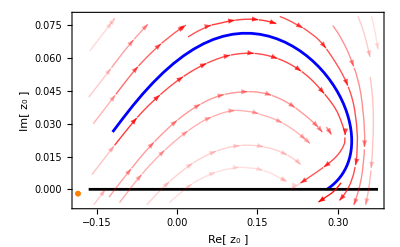

```mathematica
streamPlot[1,0.03][data]
```

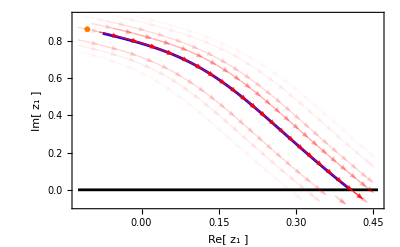

```mathematica
streamPlot[2,0.03][data]
```

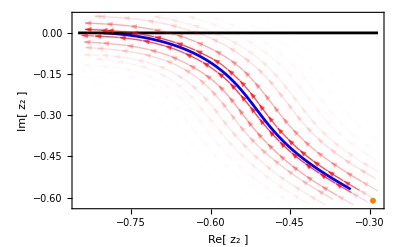

```mathematica
streamPlot[3,0.03][data]
```